```mathematica
Get["NeutronBeam/NBeam+ExB_Proton.m"]
```

$Aborted

```mathematica
xDetFTest=xDetF[0.,0.012,0.014,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.]
```

0.0410594

```mathematica
yDetFTest=yDetF[0.,0.012,0.014,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.]
```

0.0140175

```mathematica
yDVHandSolve[phiDV_,xDet_,yDet_,p_,th0_,BRxB_,rRxB_,rA_,rD_,ExBscale_,U_,phiDet_]:=(yExBGCB[yDet,p,th0,phiDet,BRxB,rRxB,rD,U]-kExB[p,ExBscale]*xExBGCB[xDet,p,th0,phiDet,BRxB,rRxB,rD,U])/(1+kExB[p,ExBscale]^2)/Sqrt[1/rA]+rG[p,th0,BRxB/rRxB]*Sin[phiDV]
```

```mathematica
yDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,0.2,1.,1.05,0.95,0.,-15000,0.]
```

0.014

```mathematica
xDVHandSolve[phiDV_,xDet_,yDet_,p_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,R_,G1_,G2_,ExBscale_,U_,phiDet_]:=
(
xExBGCB[xDet,p,th0,phiDet,BRxB,rRxB,rD,U]
+kExB[p,ExBscale]/Sqrt[1/rA]*
(
yDVHandSolve[phiDV,xDet,yDet,p,th0,BRxB,rRxB,rA,rD,ExBscale,U,phiDet]-rG[p,th0,BRxB/rRxB]*Sin[phiDV]
)
-D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,yGCAF[yDVHandSolve[phiDV,xDet,yDet,p,th0,BRxB,rRxB,rA,rD,ExBscale,U,phiDet],phiDV,p,th0,BRxB,rRxB,rA],R,G1,G2]
)/Sqrt[1/rA]+
rG[p,th0,BRxB/rRxB]*Cos[phiDV]
```

```mathematica
xDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
```

0.012

```mathematica
xDVHandSolve[phiDV,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale,U,phiDet]
```

(p rRxB Cos[phiDV] Sin[th0])/(299792458 BRxB)+1/(√(1/rA))((xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Cos[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))/(BRxB rD))/(√(rRxB/rD))+(ExBscale (20-5.47468×10^-6 p) rA (-1/(50 √(rRxB/rD))ExBscale (20-5.47468×10^-6 p) (xDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Cos[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))/(BRxB rD))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Sin[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))/(BRxB rD))/(√(rRxB/rD))))/(50 (1+(ExBscale^2 (20-5.47468×10^-6 p)^2)/2500))-(alpha p (2-rRxB Sin[th0]^2))/(599584916 √(1-rRxB Sin[th0]^2) (BRxB-(BRxB G1 (-1/(50 √(rRxB/rD))ExBscale (20-5.47468×10^-6 p) (xDet-1/(BRxB rD)3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Cos[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Sin[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))/(BRxB rD))/(√(rRxB/rD))))/((1+(ExBscale^2 (20-5.47468×10^-6 p)^2)/2500) R)+(BRxB G2 (-1/(50 √(rRxB/rD))ExBscale (20-5.47468×10^-6 p) (xDet-1/(BRxB rD)3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Cos[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))+(yDet-(3.33564×10^-9 rRxB √(5.32894×10^-10 p^2-U) Sin[phiDet] √((p^2 rD Sin[th0]^2)/(5.32894×10^-10 p^2-U)))/(BRxB rD))/(√(rRxB/rD)))^2)/((1+(ExBscale^2 (20-5.47468×10^-6 p)^2)/2500)^2 R^2))))

```mathematica
FullSimplify[xDVHandSolve[phiDV,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale,U,phiDet],Assumptions->{{p,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale}>0.,{phiDV,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale,U,phiDet}∈Reals}]
```

$Aborted

```mathematica
xDVHandSolve[0.,xDetFTest,yDetFTest,500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
```

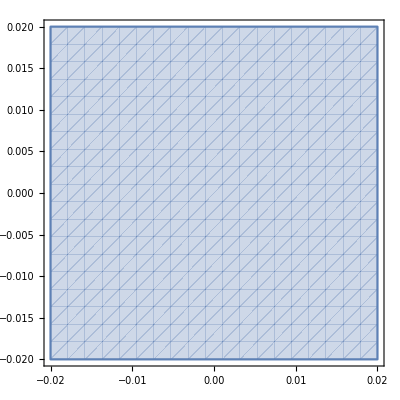

```mathematica
RegionPlot[
xDV==xDVHandSolve[0.,
xDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
yDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
500000,Pi/4,Pi,0.2,1.,1.05,0.95,1.,1.,1.,0.,-15000,0.]
&&
yDV==yDVHandSolve[0.,
xDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
yDetF[0.,xDV,yDV,500000,Pi/4,Pi,0.2,1.,1.05,1.,1.,1.,0.95,0.,-15000.,0.],
500000,Pi/4,0.2,1.,1.05,0.95,0.,-15000,0.]
,{xDV,-0.02,0.02},{yDV,-0.02,0.02}]
```

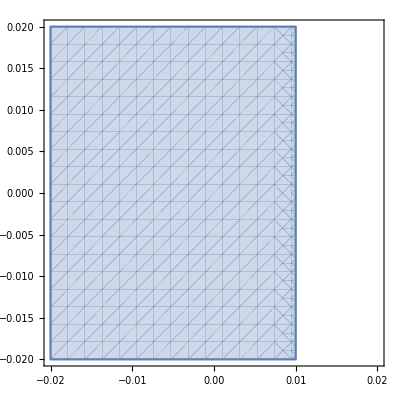

```mathematica
RegionPlot[x<0.01,{x,-0.02,0.02},{yDV,-0.02,0.02}]
```

```mathematica
?IntegrandProton2DwNBeamAccelCompiled
```

```mathematica
pmomNormedGlueck[500000,λ0,a,b]
```

```mathematica
TrapezNBeamCompiledNormed[xDVHandSolve[phiDV,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,R,G1,G2,ExBscale,U,phiDet]-xOff,{twx,plx,k1x,k2x,k3x}]*TrapezNBeamCompiledNormed[yDVHandSolve[phiDV,xDet,yDet,p,th0,BRxB,rRxB,rA,rD,ExBscale,U,phiDet]-yOff,{twy,ply,k1y,k2y,k3y}]
```

```mathematica
ApertBooleCompiled[xA[phiA,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,ExBscale,U],yA[phiA,xDet,yDet,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,ExBscale,U],xAA,yAA,xOff,yOff]
```

```mathematica
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,0.,0.,500000.,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}]
```

0.0000996278

```mathematica
Plot3D[
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,phiA,0.,p,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],
{p,0,ppmax},{phiA,-Pi,Pi}]
```

-Graphics3D-

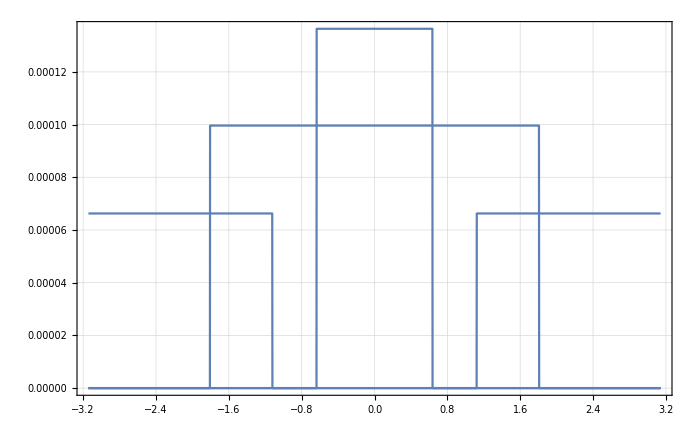

```mathematica
Plot[
Table[
IntegrandProton2DwNBeamAccelCompiled[λ0,a0,0.,0.,0.,{0.,phiA,0.,p,Pi/4},{Pi,0.2,1.,1.05,1.,1.,1.,1.,0.,-15000.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.}],{p,{3,4,5,6}*10^5}],
{phiA,-Pi,Pi}]
```